```mathematica
ClearAll["Global`*"];
SetDirectory[NotebookDirectory[]];
Directory[]
Off[Needs::nocont];Needs["LowDiscrep`"];
On[Needs::nocont];
SeedRandom[1234];
```

/Users/npadmana/myWork/lowdiscrepancyRR/mma

## Timing of LDS generation

```mathematica
Timing[generateLDSshiftedGrid[100^2,6];]
```

{0.004698,Null}

```mathematica
Timing[generateLDSshiftedGrid[1000^2,6];]
```

{0.496343,Null}

```mathematica
Timing[generateLDSshiftedGrid[2000^2,6];]
```

{2.21934,Null}

## 3D shell function

y = r^3/3, x = (r^3- r_1^3)/(r_2^3- r_1^3)

```mathematica
Clear[shellFunc];
shellFunc[rlo_, rhi_]:= Compile[{{x,_Real,1}},
Module[{r, cth,sth, ϕ, x1, y1, z1, jac},
ϕ = x[[6]]*2π;
cth = x[[5]]*2.0-1.0;
sth = Sqrt[1-cth^2];
r = (x[[4]]*(rhi^3- rlo^3)+ rlo^3)^(1/3);
x1 = x[[1]]+r*sth*Cos[ϕ];
y1 = x[[2]]+r*sth*Sin[ϕ];
z1 = x[[3]]+r*cth;
If[(x1 >0)&&(x1 < 1) && (y1 > 0) && (y1 < 1) && (z1 >0) && (z1 <1), 1.0, 0.0]
],
CompilationTarget->"C", 
RuntimeAttributes->{Listable}];
```

```mathematica
shellFuncJac[rlo_, rhi_]:= 4π (rhi^3- rlo^3)/3;
```

```mathematica
rr3dbin[rlo_, rhi_, num_]:= mcIntegrate[shellFunc[rlo,rhi],generateLDSshiftedGrid[num, 6]]*shellFuncJac[rlo,rhi];
```

```mathematica
Timing[rr3dbin[0.25,0.5,100000]]
```

{0.23168,0.227558}

```mathematica
Timing[rr3dbin[0.25,0.5,1000000]]
```

{1.29793,0.227832}

## Histograms

```mathematica
Timing[v1 = Reap[Do[Sow[rr3dbin[0.25, 0.5, 10000]],{1000}]][[2,1]];]
```

{139.984,Null}

```mathematica
Mean[v1]
```

0.227942

```mathematica
StandardDeviation[v1]/Mean[v1]
```

0.00526562

```mathematica
(* Histogram for 10000 pts *)
```

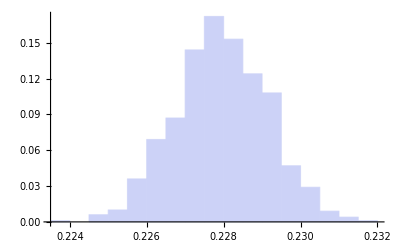

```mathematica
Histogram[v1,{0.0005}, "Probability"]
```

```mathematica
Timing[v2 = Reap[Do[Sow[rr3dbin[0.25, 0.5, 100000]],{1000}]][[2,1]];]
```

{234.791,Null}

```mathematica
Mean[v2]
```

0.227911

```mathematica
StandardDeviation[v2]/Mean[v2]
```

0.00114004

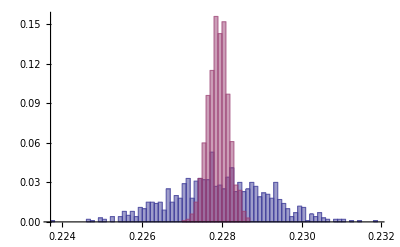

```mathematica
Histogram[{v1,v2},{0.0001}, "Probability"]
```

## Error Scaling

```mathematica
nvals = {1,2,5,10,20,50,100}*10000;
```

```mathematica
Timing[lds1=Table[getmeanerror[rr3dbin[0.25, 0.5, ii], 100], {ii, nvals}];]
```

{283.394,Null}

```mathematica
lds1
```

{{0.228063,0.00128296},{0.227853,0.000848144},{0.227915,0.000481742},{0.227873,0.000238015},{0.227935,0.000150748},{0.227918,0.0000806865},{0.227892,0.0000492241}}

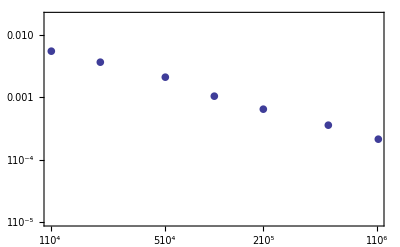

```mathematica
ListLogLogPlot[Transpose[{nvals, lds1[[All,2]]/lds1[[7,1]]}],  Frame->True, PlotMarkers->{Automatic, 10}, PlotRange->{Automatic, {1.*^-5, 0.02}}]
```

```mathematica
Fit[Log[Transpose[{nvals,  lds1[[All,2]]}]],{1,x},x]
```

0.0533699-0.72254 x